```mathematica
d=4
G[w_,L_,t_]:=Sum[
Exp[-(Pi * k * w /(2*L))^2]*
Exp[-d*(Pi*k/L)^2*t],
{k,-Infinity,Infinity}] /
Sum[
Exp[-(Pi * k * w /(2*L))^2],
{k,-Infinity,Infinity}]
```

4

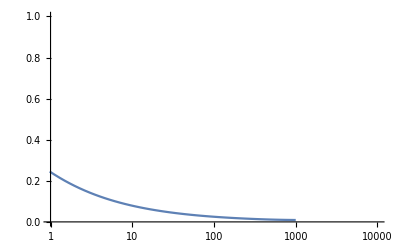

```mathematica
LogLinearPlot[G[1,100,t],{t,0,1000},
PlotRange->{{1,10000}, {0,1}}]
```

### Get an expression for a finite Fourier transform of the incoherent intermediate scattering function. FF are the fourier series elements

```mathematica
ClearAll[d,k,L,t,r]
F[r_,t_]:=1/(2*Sqrt[d*t*Pi])*Exp[-r^2/(4*d*t)]
Integrate[Exp[-I*k*r]*F[r,t],{r,-Infinity,Infinity},Assumptions-> {Re[1/(d*t)]>0,L∈Reals,L>0,d∈Reals,d>0,t∈Reals}]//FullSimplify

FF[k_,t_]:= 1/L * Integrate[Exp[-I*k*r]*F[r,t],{r,-L,L},Assumptions-> {Re[1/(d*t)]>0,L∈ Reals,L>0}]//FullSimplify
FF[k,t]
```

(ⅇ^(-d q^2 t) √(1/(d t)) √(d t))/(√(2 π))

FourierSeries[ⅇ^(-r^2/(4 d t)),r,k]/(2 √π √(d t))

### Do the same for the beam profile W(r) to get the Fourier series element W_K

```mathematica
W[r_]:=1/(w*Sqrt[Pi])Exp[-r^2/w^2]

(* Sanity check to make sure this returns the expected W(q)*)
Integrate[Exp[-I*k*r]*W[r],{r,-Infinity,Infinity},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]

FW[k_]:=1/L*Integrate[Exp[-I*k*r]*W[r],{r,-L,L},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]
FW[k]
```

ⅇ^(-1/4 k^2 w^2)

(ⅇ^(-1/4 k^2 w^2) (Erf[L/w-(ⅈ k w)/2]+Erf[L/w+(ⅈ k w)/2]))/(2 L)

### Now combine them, to get the spatially-limited autocorrelation G(t;w;L)

```mathematica
ClearAll[L,w,t,k]
```

```mathematica
G[t_,W_,l_,BOUND_:1]:=
Sum[
Abs[FW[k]]^2 * FF[k,t]
,{k,-BOUND,BOUND}]/
Sum[
Abs[FW[k]]^2 * FF[k,tp]
,{k,-BOUND,BOUND}]/.{L->l,w->W}//Chop
```

Make a compiled version of the function. Runs much faster.

```mathematica
Gc=Compile[{t,w,l},Sum[
Abs[FW[k]]^2 * FF[k,t]
,{k,-1,1}]/
Sum[
Abs[FW[k]]^2 * FF[k,tp]
,{k,-1,1}]/.{L->l,w->W} // Chop];
```

```mathematica
fullForm=G[t,w,L];
```

Extract some values of the autocorrelation curve

```mathematica
Gc[10,10,100]//N
```

1.

```mathematica
G[10000,10,100]/.{L->1,d->1,w->1,tp->.0000000000001}//N
(*Took 143s to evaluate. In the denominator of this, you can see a division by tp, but tp should be zero.*)
```

0.276326+0. ⅈ

Make a table for a few values of the autocorrelation, useful for checking it.

```mathematica
d=4;
w=10
L=10
tp=1*^-10;
Table[G[t,10,100,1],{t,1,10000,2000}]//N
```

{1.+0. ⅈ,0.570689+0. ⅈ,0.423802+0. ⅈ,0.351896+0. ⅈ,0.307349+0. ⅈ}

Make a table using different values of the limits for the sum

```mathematica
w=20
L=5
Table[
Table[G[t,w,L,B],{t,1,10000,2000}]//N
,{B,1,5}]
```

20

5

{{0.861185+0. ⅈ,0.029089+0. ⅈ,0.0205742+0. ⅈ,0.0168002+0. ⅈ,0.01455+0. ⅈ},{0.856944+0. ⅈ,0.0289386+0. ⅈ,0.0204678+0. ⅈ,0.0167133+0. ⅈ,0.0144748+0. ⅈ},{0.854191+0. ⅈ,0.0288483+0. ⅈ,0.020404+0. ⅈ,0.0166612+0. ⅈ,0.0144296+0. ⅈ},{0.851223+0. ⅈ,0.0287517+0. ⅈ,0.0203357+0. ⅈ,0.0166054+0. ⅈ,0.0143813+0. ⅈ},{0.851179+0. ⅈ,0.0287502+0. ⅈ,0.0203346+0. ⅈ,0.0166046+0. ⅈ,0.0143806+0. ⅈ}}

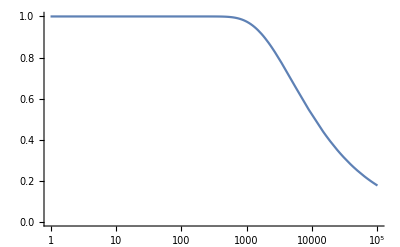

```mathematica
d=1;
L=100;
w=20;
tp=1*^-10;
Show[
LogLinearPlot[Gc[t,w,L],{t,1,1*^5},PerformanceGoal->"Speed",GridLines->{{w^2/(4*d)},{0.5}}],PlotRange->{0,1}]
```

```mathematica
ClearAll[L,w]
w=20;
L=100;
FindRoot[Re[G[t,w,L]]-0.5,{t,100}]
w^2/(4*d)
```

{t→2747.64}

25

```mathematica
FF[k,t]//PowerExpand
(*The argument to Erf has an L/(2*Sqrt{d*t}) which is problematic at t=0*)
```

(ⅇ^(-d k^2 t) (Erf[(L-2 ⅈ d k t)/(2 √d √t)]+Erf[(L+2 ⅈ d k t)/(2 √d √t)]))/(2 L)

#### Scratch

```mathematica
Integrate[Exp[-r*(I*q+r/(4*D*t))],{r,-Infinity,Infinity}]/. 
  Erf[x_] :> 2/Sqrt[π] HoldForm[Integrate[E^-r^2, {r, 0, x}]]
```

ConditionalExpression[(2 ⅇ^(-D q^2 t) √π)/(√(1/(D t))),Re[1/(D t)]>0]